```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/IR_RAMAN/ZrC"];
zrcIR=Table[ReadList[{"initial_kp444_encut700-ENCUT_500_ediff6-PERF","initial_kp444_encut700-ENCUT_500_ediff6-FREN"}[[i]],{Number,Number,Number}],{i,1,2}];
```

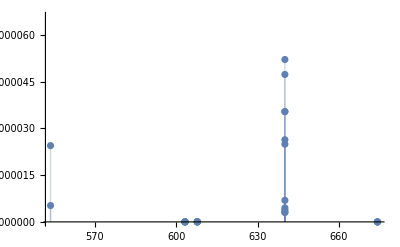

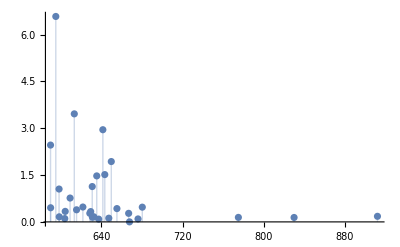

```mathematica
dataPerf=Transpose@{Transpose[zrcIR[[1]]][[2]],Transpose[zrcIR[[1]]][[3]]};
dataFren=Transpose@{Transpose[zrcIR[[2]]][[2]],Transpose[zrcIR[[2]]][[3]]};
ListPlot[dataPerf,Filling->Axis]
ListPlot[dataFren,Filling->Axis,PlotRange->All]
```

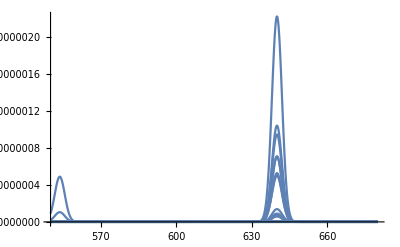

```mathematica
plotFun[{m_,h_}]:=Plot[h*PDF[NormalDistribution[m,2],x],{x,550,680},PlotRange->All]
Show[Table[plotFun[dataPerf[[i]]],{i,1,30}]]
```

```mathematica
gauss[{m_,h_}]:=h*PDF[NormalDistribution[m,2],x]
```

```mathematica
Total@Table[gauss[dataPerf[[i]]],{i,1,3}]
p1=Plot[2-Total[Table[gauss[dataPerf[[i]]],{i,1,30}]],{x,500,900},Ticks->{Automatic,None},PlotRange->All,PlotLabel->"Predicted pristine bulk ZrC IR spectrum",AxesLabel->{"Energy (1/cm)","Intensity (au)"},ImageSize->550];
```

6.49048×10^-11 ⅇ^(-1/8 (-674.168+x)^2)+5.75474×10^-12 ⅇ^(-1/8 (-674.168+x)^2)+2.27078×10^-11 ⅇ^(-1/8 (-674.168+x)^2)

```mathematica
Total@Table[gauss[dataFren[[i]]],{i,1,3}]
p2=Plot[2-Total[Table[gauss[dataFren[[i]]],{i,1,30}]],{x,500,900},Ticks->{Automatic,None},PlotRange->All,PlotLabel->"Predicted Frenkel defective bulk ZrC IR spectrum",AxesLabel->{"Energy (1/cm)","Intensity (au)"},ImageSize->550];
```

0.0356469 ⅇ^(-1/8 (-912.15+x)^2)+0.0281952 ⅇ^(-1/8 (-829.926+x)^2)+0.0287568 ⅇ^(-1/8 (-775.001+x)^2)

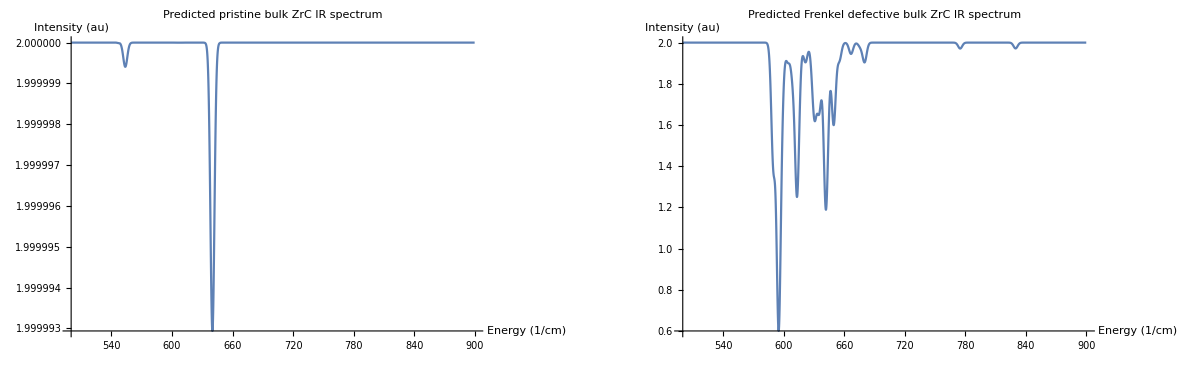

```mathematica
GraphicsGrid[{{p1,p2}}]
```